```mathematica
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
mag1 = radObjRecMag[{-300*^-6,0,100*^-6},{100*^-6,100*^-6,100*^-6},{1,0,0}];
mag2= radObjRecMag[{300*^-6,0,100*^-6},{100*^-6,100*^-6,100*^-6},{1,0,0}];
```

```mathematica
magnetContainer =radObjCnt[{mag1,mag2}];
```

```mathematica
Show[Graphics3D[radObjDrw[magnetContainer]]]
```

-Graphics3D-

```mathematica
DensityPlot[radFld[magnetContainer,"bx",{x,y,-10*^-6}],{x,-300*^-6,300*^-6},{y,-100*^-6,100*^-6},PlotLegends->Automatic]
```

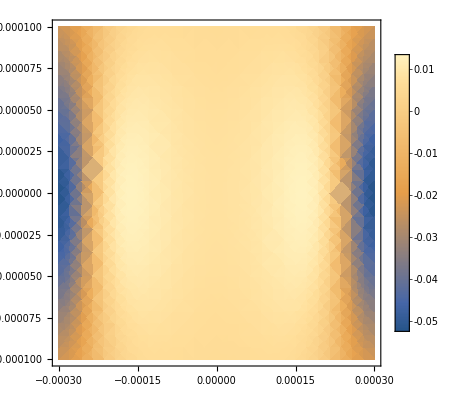
```mathematica
-Graphics-B_x(T)
```

```mathematica
DensityPlot[radFld[magnetContainer,"by",{x,y,-10*^-6}],{x,-300*^-6,300*^-6},{y,-100*^-6,100*^-6},PlotLegends->Automatic]
```

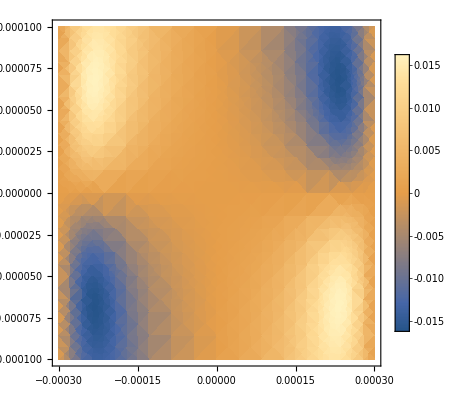
```mathematica
-Graphics-B_y(T)
```

```mathematica
DensityPlot[radFld[magnetContainer,"bz",{x,y,-10*^-6}],{x,-300*^-6,300*^-6},{y,-100*^-6,100*^-6},PlotLegends->Automatic]
```

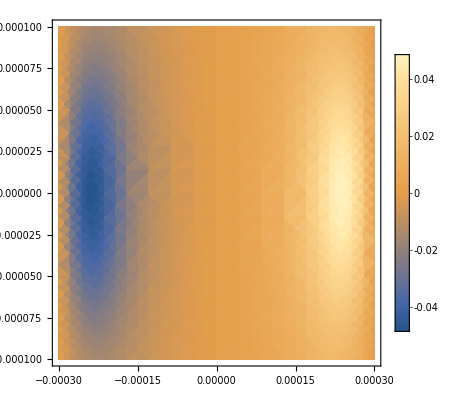
```mathematica
-Graphics-B_z(T)
```